# Abductive reasoning

## Global conditions

```mathematica
Clear["Global`*"]
r=3;
ϵ=(1-e1)*(1-e2)+e1*e2;
e=e2;
(*ternary coords where x corresponds to freq alld, y to freq allc *)
TernCoords[x_,y_]={{1/2,-1/2},{-Tan[Pi/3]/2,-Tan[Pi/3]/2}}.{x,y}+{1/2,Tan[Pi/3]/2};
diskradius=.015;
textoffset=.05;
thickness=.005;
vlabels={Graphics[Text[Style["AllD",FontSize->Large],{-textoffset,-textoffset}]],Graphics[Text[Style["AllC",FontSize->Large],{1+textoffset,-textoffset}]],Graphics[Text[Style["Disc",FontSize->Large],{1/2,Tan[Pi/3]/2+textoffset}]]};
SetDirectory["/Users/brycemorsky/Desktop/New projects/Indirect reciprocity/abduction/figures"];
```

## Scoring

### Ternary plot

```mathematica
T=10000;
g=x*gx+y*gy+(1-x-y)*gz;
(* World 1: B ∅ *)
w1=0;
(* World 2: B -> *)
w21=(1-g)*ψ*e; 
w24=g*(1-ψ)*ϵ;
w2=FullSimplify[w24/(w21+w24)];
(* World 3: G ∅ *)
w31=(1-g)*(1-ψ)*(1-e); 
w34=g*ψ*(1-ϵ);
w3=FullSimplify[w34/(w31+w34)];
(* World 4: G -> *)
w4=1;
Qbd=(1-e)*w1+e*w2;
Qbc=ϵ*w2+(1-ϵ)*w1;
Qgd=(1-e)*w3+e*w4;
Qgc=ϵ*w4+(1-ϵ)*w3;
ψ=0.5;
(*Qbd=0;
Qbc=0;
Qgd=1;
Qgc=1;*)
repsys={
0==(1-gx)*Qbc - gx*(1-Qgc),
0==(1-gy)*Qbd - gy*(1-Qgd),
0==(1-gz)*(g*Qbc+(1-g)*Qbd)-gz*(g*(1-Qgc)+(1-g)*(1-Qgd))
}/.{e->0.01,e1->0.01,e2->0.01,ϵ-> 0.99^2+0.01^2};
M=Array[m,{5151,5}];
count=1;
Do[
M[[count]]= {0.01*i,0.01*j,gx,gy,gz}/.FindRoot[repsys/.{x->0.01*i,y->0.01*j},{{gx,0.9},{gy,0.1},{gz,0.6}}];
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==Evaluate[(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]})],
y'[t]==Evaluate[(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]})],
gx'[t]==10000*Evaluate[((1-gx)*Qbc - gx*(1-Qgc))/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}],
gy'[t]==10000*Evaluate[((1-gy)*Qbd - gy*(1-Qgd))/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}],
gz'[t]==10000*Evaluate[((1-gz)*(g*Qbc+(1-g)*Qbd)-gz*(g*(1-Qgc)+(1-g)*(1-Qgd)))/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}]
}/.{e->0.01,e1->0.01,e2->0.01,ϵ-> 0.99^2+0.01^2};
Eqstable=Array[m,{4851,2}];
count1 = 1;
Do[
(*{icgx,icgy,icgz}={gx,gy,gz}/.FindRoot[repsys/.{x->0.01*i,y->0.01*j},{{gx,0.95},{gy,0.01},{gz,0.7}}];*)
R=NDSolve[Join[fullsys,{x[0]==0.01*i,y[0]==0.01*j,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Eqstable[[count1]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count1=count1+1;
,{i,1,98},{j,1,99-i}];
N
dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageScoring=Show[ternplot,dots,vlabels, ImageSize-> Large,PlotRangePadding->.1];;
Export["scoring_psi05.pdf",imageScoring];
```

```mathematica
T=10000;
g=x*gx+y*gy+(1-x-y)*gz;
(* World 1: B ∅ *)
w1=0;
(* World 2: B -> *)
w21=(1-g)*ψ*e; 
w24=g*(1-ψ)*ϵ;
w2=FullSimplify[w24/(w21+w24)];
(* World 3: G ∅ *)
w31=(1-g)*(1-ψ)*(1-e); 
w34=g*ψ*(1-ϵ);
w3=FullSimplify[w34/(w31+w34)];
(* World 4: G -> *)
w4=1;
Qbd=(1-e)*w1+e*w2;
Qbc=ϵ*w2+(1-ϵ)*w1;
Qgd=(1-e)*w3+e*w4;
Qgc=ϵ*w4+(1-ϵ)*w3;
ψ=0.5;
(*Qbd=0;
Qbc=0;
Qgd=1;
Qgc=1;*)
repsys={
0==(1-gx)*Qbc - gx*(1-Qgc),
0==(1-gy)*Qbd - gy*(1-Qgd),
0==(1-gz)*(g*Qbc+(1-g)*Qbd)-gz*(g*(1-Qgc)+(1-g)*(1-Qgd))
}/.{e->0.01,e1->0.01,e2->0.01,ϵ-> 0.99^2+0.01^2};
M=Array[m,{5151,5}];
count=1;
Do[
M[[count]]= {0.01*i,0.01*j,gx,gy,gz}/.FindRoot[repsys/.{x->0.01*i,y->0.01*j},{{gx,0.9},{gy,0.1},{gz,0.6}}];
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==Evaluate[(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]})],
y'[t]==Evaluate[(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]})],
gx'[t]==10000*Evaluate[((1-gx)*Qbc - gx*(1-Qgc))/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}],
gy'[t]==10000*Evaluate[((1-gy)*Qbd - gy*(1-Qgd))/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}],
gz'[t]==10000*Evaluate[((1-gz)*(g*Qbc+(1-g)*Qbd)-gz*(g*(1-Qgc)+(1-g)*(1-Qgd)))/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}]
}/.{e->0.01,e1->0.01,e2->0.01,ϵ-> 0.99^2+0.01^2};
Eqstable=Array[m,{4851,2}];
count1 = 1;
Do[
(*{icgx,icgy,icgz}={gx,gy,gz}/.FindRoot[repsys/.{x->0.01*i,y->0.01*j},{{gx,0.95},{gy,0.01},{gz,0.7}}];*)
R=NDSolve[Join[fullsys,{x[0]==0.01*i,y[0]==0.01*j,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Eqstable[[count1]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count1=count1+1;
,{i,1,98},{j,1,99-i}];
N
dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageScoring=Show[ternplot,dots,vlabels, ImageSize-> Large,PlotRangePadding->.1];;
Export["scoring_psi05.pdf",imageScoring];
```

### Stability analysis

```mathematica
Clear["Global`*"]
g=x*gx+y*gy+(1-x-y)*gz;
(* World 1: B ∅ *)
w1=0;
(* World 2: B -> *)
w21=(1-g)*ψ*e; 
w24=g*(1-ψ)*ϵ;
w2=w24/(w21+w24);
(* World 3: G ∅ *)
w31=(1-g)*(1-ψ)*(1-e); 
w34=g*ψ*(1-ϵ);
w3=w34/(w31+w34);
(* World 4: G -> *)
w4=1;
Qbd=e*w2;
Qbc=ϵ*w2;
Qgd=(1-e)*w3+e;
Qgc=ϵ+(1-ϵ)*w3;
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
A={x*(pix-pi),
y*(piy-pi),
τ*((1-gx)*Qbc - gx*(1-Qgc)),
τ*((1-gy)*Qbd - gy*(1-Qgd)),
τ*((1-gz)*(g*Qbc+(1-g)*Qbd)-gz*(g*(1-Qgc)+(1-g)*(1-Qgd)))
};
J=FullSimplify[D[A,{{x,y,gx,gy,gz}}]/.{x->0,y->1-z,gx->0,gy->0,gz->0}]
Eigensystem[J]
```

## Shunning

```mathematica
T=1000000;
ψ=0.5;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* World 1: B ∅ B *)
w1=0;
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=0;
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ;
w43=(1-g)*ψ*ϵ*(1-g)*(1-ψ);
w48=g*(1-ψ)*ϵ*g*ψ;
w4=Simplify[w48/(w42+w43+w48)];
(* World 5: G ∅ B *)
w5=0;
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w68=g*ψ*(1-ϵ)*g*ψ;
w6=Simplify[w68/(w62+w68)];
(* World 7: G -> B *)
w73=(1-g)*(1-ψ)*ϵ*(1-g)*ψ;
w78=g*ψ*ϵ*g*(1-ψ);
w7=Simplify[w78/(w73+w78)];
(* World 8: G -> G *)
w8=1;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;
repsys={
gx'[t]==Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t],
gy'[t]==Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t],
gz'[t]==Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t]
};
M=Array[m,{66,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.1*i,y->0.1*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,100}];
M[[count]]= {0.1*i,0.1*j,gx[100]/.R[[1]],gy[100]/.R[[1]],gz[100]/.R[[1]]};
count=count+1;
,{i,0,10},{j,0,10-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{4851,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.01*i,y[0]==0.01*j,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Eqstable[[count]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count=count+1;
,{i,1,98},{j,1,99-i}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageShunning=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["shunning.pdf",imageShunning];
```

## Simple standing

### Public assessment

#### Ternary plot

```mathematica
T=1000000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* World 1: B ∅ B *)
w12=(1-g)*ψ*(1-e)*g*(1-ψ); 
w15=g*(1-ψ)*(1-e)*(1-g)*ψ;
w1=Simplify[w15/(w12+w15)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=1;
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w48=g*(1-ψ)*ϵ*g*ψ;
w4=Simplify[w48/(w42+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w65=g*ψ*(1-e)*(1-g)*(1-ψ);
w68=g*ψ*(1-ϵ)*g*ψ;
w6=Simplify[(w65+w68)/(w62+w65+w68)];
(* World 7: G -> B *)
w7=1;
(* World 8: G -> G *)
w8=1;
ψ=0.5;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;
repsys={
gx'[t]==Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t],
gy'[t]==Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t],
gz'[t]==Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t]
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,T}];
M[[count]]= {0.01*i,0.01*j,gx[T]/.R[[1]],gy[T]/.R[[1]],gz[T]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{5151,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.01*i,y[0]==0.01*j,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Eqstable[[count]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSimplestanding=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["public_simple_standing_psi05.pdf",imageSimplestanding];
```

#### Heat maps

```mathematica
T=100000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* World 1: B ∅ B *)
w12=(1-g)*ψ*(1-e)*g*(1-ψ); 
w15=g*(1-ψ)*(1-e)*(1-g)*ψ;
w1=Simplify[w15/(w12+w15)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=1;
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w48=g*(1-ψ)*ϵ*g*ψ;
w4=Simplify[w48/(w42+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w65=g*ψ*(1-e)*(1-g)*(1-ψ);
w68=g*ψ*(1-ϵ)*g*ψ;
w6=Simplify[(w65+w68)/(w62+w65+w68)];
(* World 7: G -> B *)
w7=1;
(* World 8: G -> G *)
w8=1;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;

pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;

repsysBayes={
gx'[t]==Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t],
gy'[t]==Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t],
gz'[t]==Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t]
};
fullsysBayes={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*(Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*(Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*(Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};

repsysNonreason={
gx'[t]==(1-g)*(1-e2)+g*ϵ-gx[t],
gy'[t]==(1-g)*(1-e2)+g*e2-gy[t],
gz'[t]==(1-g)*(1-e2)+ϵ*g-gz[t]
};
fullsysNonreason={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*((1-g)*(1-e2)+g*ϵ-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*((1-g)*(1-e2)+g*e2-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*((1-g)*(1-e2)+ϵ*g-gz[t])/.{x->x[t],y->y[t]})
};

count=1;
basinBayesPsi25=Array[m,{100,3}];
basinBayesPsi5=Array[m,{100,3}];
basinBayesPsi75=Array[m,{100,3}];
basinNonreason=Array[m,{100,3}];

Do[
mysumBayesPsi25 = 0;
mysumBayesPsi5 = 0;
mysumBayesPsi75 = 0;
mysumNonreason= 0;

repsysBayesPsi25=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
fullsysBayesPsi25=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
repsysBayesPsi5=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
fullsysBayesPsi5=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
repsysBayesPsi75=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
fullsysBayesPsi75=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
repsys2=repsysNonreason/.{e1->ii/50,e2->jj/50};
fullsys2=fullsysNonreason/.{e1->ii/50,e2->jj/50};

Do[
{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi25/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi25=NDSolve[Join[fullsysBayesPsi25,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi5/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi5=NDSolve[Join[fullsysBayesPsi5,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi75/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi75=NDSolve[Join[fullsysBayesPsi75,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsys2/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RNonreason=NDSolve[Join[fullsys2,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

mysumBayesPsi25=mysumBayesPsi25+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi25[[1]]];
mysumBayesPsi5=mysumBayesPsi5+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi5[[1]]];
mysumBayesPsi75=mysumBayesPsi75+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi75[[1]]];
mysumNonreason=mysumNonreason+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RNonreason[[1]]];
,{i,1,4},{j,1,5-i}];
basinBayesPsi25[[count]]={ii/50,jj/50,mysumBayesPsi25/10};
basinBayesPsi5[[count]]={ii/50,jj/50,mysumBayesPsi5/10};
basinBayesPsi75[[count]]={ii/50,jj/50,mysumBayesPsi75/10};
basinNonreason[[count]]={ii/50,jj/50,mysumNonreason/10};
count=count+1;
,{ii,1,10},{jj,1,10}];

colfunc=(ColorData["SunsetColors"][Rescale[#,{0.6,0}]]&);

imageSSpublicBayesPsi25=Show[ListDensityPlot[basinBayesPsi25,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SS abduction ψ=0.25"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSSpublicBayesPsi5=Show[ListDensityPlot[basinBayesPsi5,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SS abduction ψ=0.5"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSSpublicBayesPsi75=Show[ListDensityPlot[basinBayesPsi75,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SS abduction ψ=0.75"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSSpublicNonreason=Show[ListDensityPlot[basinNonreason,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SS non-reasoning"}},LabelStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
```

### Private assessment

#### Ternary plot

```mathematica
T=1000000;
e1=0.01;
e2=0.01;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
(* World 1: B ∅ B *)
w12=(1-g)*ψ*(1-e)*g*(1-ψ); 
w15=g*(1-ψ)*(1-e)*(1-g)*ψ;
w1=Simplify[w15/(w12+w15)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=1;
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w48=g*(1-ψ)*ϵ*g*ψ;
w4=Simplify[w48/(w42+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w65=g*ψ*(1-e)*(1-g)*(1-ψ);
w68=g*ψ*(1-ϵ)*g*ψ;
w6=Simplify[(w65+w68)/(w62+w65+w68)];
(* World 7: G -> B *)
w7=1;
(* World 8: G -> G *)
w8=1;
ψ=0.5;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;
repsys={
gx'[t]==(1-gx[t])*(Qbcg*g+Qbcb*(1-g))-gx[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)),
gy'[t]==(1-gy[t])*(Qbdg*g+Qbdb*(1-g))-gy[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)),
gz'[t]==(1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2*g+g2))-gz[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)),
gx2'[t]==(gx[t]-gx2[t])*(Qbcg*g+Qbcb*(1-g))-gx2[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)),
gy2'[t]==(gy[t]-gy2[t])*(Qbdg*g+Qbdb*(1-g))-gy2[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)),
gz2'[t]==(gz[t]-gz2[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb*(1-2*g+g2))-gz2[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2))
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}];
M[[count]]= {0.01*i,0.01*j,gx[T]/.R[[1]],gy[T]/.R[[1]],gz[T]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*((1-gx[t])*(Qbcg*g+Qbcb*(1-g))-gx[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)))/.{x->x[t],y->y[t]}),
gy'[t]==(10000*((1-gy[t])*(Qbdg*g+Qbdb*(1-g))-gy[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)))/.{x->x[t],y->y[t]}),
gz'[t]==(10000*((1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2*g+g2))-gz[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)))/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*((gx[t]-gx2[t])*(Qbcg*g+Qbcb*(1-g))-gx2[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)))/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*((gy[t]-gy2[t])*(Qbdg*g+Qbdb*(1-g))-gy2[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)))/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*((gz[t]-gz2[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb*(1-2*g+g2))-gz2[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)))/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{4851,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.01*i,y[0]==0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching"];
Eqstable[[count]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count=count+1;
,{i,1,98},{j,1,99-i}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSimpleStanding=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["private_simple_standing_psi05_e1_01_e2_01.pdf",imageSimpleStanding];
```

#### Heat map

NDSolve::overdet: There are fewer dependent variables, {gx[t],gy[t],gz[t]}, than equations, so the system is overdetermined.

ReplaceAll::reps: {0==0.05[t] (-1+3 (0.05[t]+Plus[«2»] gx[«1»])-0.05[t] (-1+3 Plus[«2»])-3 0.05[t] (0.05[t]+Plus[«2»] gy[«1»])-(1-2 0.05[«1»]) (-0.05[«1»] gx[«1»]-0.05[«1»] gy[«1»]-Plus[«2»] gz[«1»]+3 Plus[«2»])),0==0.05[t] (-0.05[t] (-1+3 Plus[«2»])+3 (0.05[t]+Plus[«2»] gy[«1»])-3 0.05[t] (0.05[t]+Plus[«2»] gy[«1»])-(1-2 0.05[«1»]) (-0.05[«1»] gx[«1»]-0.05[«1»] gy[«1»]-Plus[«2»] gz[«1»]+3 Plus[«2»])),«4»,gy[0]==0.5,gz[0]==0.5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {icgx,icgy,icgz} and {gx[100000],gy[100000],gz[100000]}/.{0==0.05[t] (-1+3 (0.05[«1»]+Times[«2»])-0.05[t] (-1+Times[«2»])-3 0.05[t] (0.05[«1»]+Times[«2»])-(1+Times[«2»]) (Times[«3»]+Times[«3»]+Times[«3»]+Times[«2»])),0==0.05[t] (-0.05[t] (-1+Times[«2»])+3 (0.05[«1»]+Times[«2»])-3 0.05[t] (0.05[«1»]+Times[«2»])-(1+Times[«2»]) (Times[«3»]+Times[«3»]+Times[«3»]+Times[«2»])),«4»,gy[0]==0.5,gz[0]==0.5} are not the same shape.

NDSolve::overdet: There are fewer dependent variables, {gx[t],gy[t],gz[t]}, than equations, so the system is overdetermined.

ReplaceAll::reps: {0==0.05[t] (-1+3 (0.05[t]+Plus[«3»] gx[«1»])-0.05[t] (-1+3 Plus[«2»])-3 0.1[t] (0.05[t]+Plus[«3»] gy[«1»])-(1-0.05[«1»]-0.1[«1»]) (-0.05[«1»] gx[«1»]-0.1[«1»] gy[«1»]-Plus[«3»] gz[«1»]+3 Plus[«2»])),0==0.1[t] (-0.05[t] (-1+3 Plus[«2»])+3 (0.05[t]+Plus[«3»] gy[«1»])-3 0.1[t] (0.05[t]+Plus[«3»] gy[«1»])-(1-0.05[«1»]-0.1[«1»]) (-0.05[«1»] gx[«1»]-0.1[«1»] gy[«1»]-Plus[«3»] gz[«1»]+3 Plus[«2»])),«4»,gy[0]==0.5,gz[0]==0.5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {icgx,icgy,icgz} and {gx[100000],gy[100000],gz[100000]}/.{0==0.05[t] (-1+3 (0.05[«1»]+Times[«2»])-0.05[t] (-1+Times[«2»])-3 0.1[t] (0.05[«1»]+Times[«2»])-(1+Times[«2»]+Times[«2»]) (Times[«3»]+Times[«3»]+Times[«3»]+Times[«2»])),0==0.1[t] (-0.05[t] (-1+Times[«2»])+3 (0.05[«1»]+Times[«2»])-3 0.1[t] (0.05[«1»]+Times[«2»])-(1+Times[«2»]+Times[«2»]) (Times[«3»]+Times[«3»]+Times[«3»]+Times[«2»])),«4»,gy[0]==0.5,gz[0]==0.5} are not the same shape.

NDSolve::overdet: There are fewer dependent variables, {gx[t],gy[t],gz[t]}, than equations, so the system is overdetermined.

General::stop: Further output of NDSolve::overdet will be suppressed during this calculation.

ReplaceAll::reps: {0==0.05[t] (-1+3 (0.05[t]+Plus[«3»] gx[«1»])-0.05[t] (-1+3 Plus[«2»])-3 0.15[t] (0.05[t]+Plus[«3»] gy[«1»])-(1-0.05[«1»]-0.15[«1»]) (-0.05[«1»] gx[«1»]-0.15[«1»] gy[«1»]-Plus[«3»] gz[«1»]+3 Plus[«2»])),«6»,gz[0]==0.5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {icgx,icgy,icgz} and {gx[100000],gy[100000],gz[100000]}/.{0==0.05[t] (-1+3 (0.05[«1»]+Times[«2»])-0.05[t] (-1+Times[«2»])-3 0.15[t] (0.05[«1»]+Times[«2»])-(1+Times[«2»]+Times[«2»]) (Times[«3»]+Times[«3»]+Times[«3»]+Times[«2»])),0==0.15[t] (-0.05[t] (-1+Times[«2»])+3 (0.05[«1»]+Times[«2»])-3 0.15[t] (0.05[«1»]+Times[«2»])-(1+Times[«2»]+Times[«2»]) (Times[«3»]+Times[«3»]+Times[«3»]+Times[«2»])),«4»,gy[0]==0.5,gz[0]==0.5} are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

$Aborted

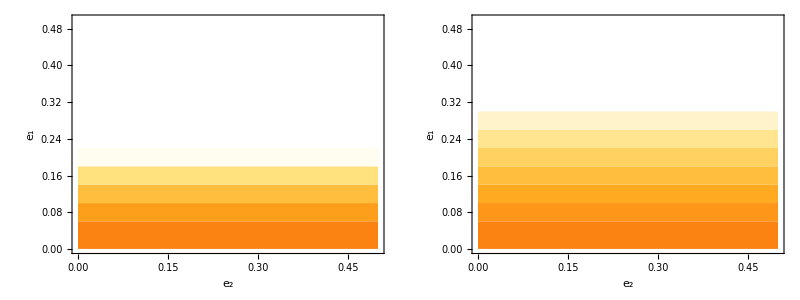

## Staying

### Public assessment

#### Ternary plot

```mathematica
T=1000000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* World 1: B ∅ B *)
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w48=g*(1-ψ)*ϵ*g*ψ;
w4=FullSimplify[w48/(w42+w48)];
(* World 5: G ∅ B *)
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w68=g*ψ*(1-ϵ)*g*ψ;
w6=FullSimplify[w68/(w62+w68)];
(* World 7: G -> B *)
(* World 8: G -> G *)
w8=1;
ψ=0.5;
Qbdg=(1-e)*w2+e*w4;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdg=(1-e)*w6+e*w8;
Qgcg=ϵ*w8+(1-ϵ)*w6;
repsys={
gx'[t]==Qgcg*gx[t]+Qbcg*(1-gx[t])-gx[t],
gy'[t]==Qgdg*gy[t]+Qbdg*(1-gy[t])-gy[t],
gz'[t]==Qgcg*gz[t]+Qbcg*(1-gz[t])-gz[t]
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,T}];
M[[count]]= {0.01*i,0.01*j,gx[T]/.R[[1]],gy[T]/.R[[1]],gz[T]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qgcg*gx[t]+Qbcg*(1-gx[t])-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qgdg*gy[t]+Qbdg*(1-gy[t])-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qgcg*gz[t]+Qbcg*(1-gz[t])-gz[t])/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{4851,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.01*i,y[0]==0.01*j,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Eqstable[[count]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count=count+1;
,{i,1,98},{j,1,99-i}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageStaying=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["public_staying_psi01.pdf",imageStaying];
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {x'[t]==x[t] (-1-x[t] (-1+3 Plus[«2»])+3 (x[t]+gx[«1»] Plus[«3»])-3 (x[t]+gy[«1»] Plus[«3»]) y[t]-(1-x[«1»]-y[«1»]) (-gx[«1»] x[«1»]+3 Plus[«2»]-gz[«1»] Plus[«3»]-gy[«1»] y[«1»])),y'[t]==y[t] (-x[t] (-1+3 Plus[«2»])+3 (x[t]+gy[«1»] Plus[«3»])-3 (x[t]+gy[«1»] Plus[«3»]) y[t]-(1-x[«1»]-y[«1»]) (-gx[«1»] x[«1»]+3 Plus[«2»]-gz[«1»] Plus[«3»]-gy[«1»] y[«1»])),«6»,gy[0]==0.5,gz[0]==0.5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {x'[t]==x[t] (-1-x[t] (-1+3 Plus[«2»])+3 (x[t]+gx[«1»] Plus[«3»])-3 (x[t]+gy[«1»] Plus[«3»]) y[t]-(1-x[«1»]-y[«1»]) (-gx[«1»] x[«1»]+3 Plus[«2»]-gz[«1»] Plus[«3»]-gy[«1»] y[«1»])),y'[t]==y[t] (-x[t] (-1+3 Plus[«2»])+3 (x[t]+gy[«1»] Plus[«3»])-3 (x[t]+gy[«1»] Plus[«3»]) y[t]-(1-x[«1»]-y[«1»]) (-gx[«1»] x[«1»]+3 Plus[«2»]-gz[«1»] Plus[«3»]-gy[«1»] y[«1»])),«6»,gy[0]==0.5,gz[0]==0.5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

$Aborted

ReplaceAll::reps: {gx'[t]==-1. gx[t]+gx[t] ((1.+Times[«2»]) (1.+Times[«2»])+e1 e2+(0.25 (e1+e2+Times[«3»]) (1.+Times[«3»]+Times[«3»]) (0.+Times[«2»]+Times[«2»]))/Plus[«2»])+(0.25 ((1.+Times[«2»]) (1.+Times[«2»])+e1 e2) (1.-1. e2+e1 (-1.+Times[«2»])) (1.-1. gx[t]) (0.+0.01 gy[t]+0.99 gz[t]))/(-0.25 e2 Plus[«3»]+0.25 Plus[«3»] Plus[«3»]),«4»,gz[0]==0.5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

#### Heat maps

```mathematica
T=100000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* World 1: B ∅ B *)
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w48=g*(1-ψ)*ϵ*g*ψ;
w4=FullSimplify[w48/(w42+w48)];
(* World 5: G ∅ B *)
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w68=g*ψ*(1-ϵ)*g*ψ;
w6=FullSimplify[w68/(w62+w68)];
(* World 7: G -> B *)
(* World 8: G -> G *)
w8=1;
Qbdg=(1-e)*w2+e*w4;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdg=(1-e)*w6+e*w8;
Qgcg=ϵ*w8+(1-ϵ)*w6;

pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;

repsysBayes={
gx'[t]==Qgcg*gx[t]+Qbcg*(1-gx[t])-gx[t],
gy'[t]==Qgdg*gy[t]+Qbdg*(1-gy[t])-gy[t],
gz'[t]==Qgcg*gz[t]+Qbcg*(1-gz[t])-gz[t]
};
fullsysBayes={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qgcg*gx[t]+Qbcg*(1-gx[t])-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qgdg*gy[t]+Qbdg*(1-gy[t])-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qgcg*gz[t]+Qbcg*(1-gz[t])-gz[t])/.{x->x[t],y->y[t]})
};

repsysNonreason={
gx'[t]==g*ϵ-g*gx[t],
gy'[t]==g*e2-g*gy[t],
gz'[t]==ϵ*g-g*gz[t]
};
fullsysNonreason={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*(g*ϵ-g*gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*(g*e2-g*gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*(ϵ*g-g*gz[t])/.{x->x[t],y->y[t]})
};

count=1;
basinBayesPsi25=Array[m,{100,3}];
basinBayesPsi5=Array[m,{100,3}];
basinBayesPsi75=Array[m,{100,3}];
basinNonreason=Array[m,{100,3}];

Do[
mysumBayesPsi25 = 0;
mysumBayesPsi5 = 0;
mysumBayesPsi75 = 0;
mysumNonreason= 0;

repsysBayesPsi25=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
fullsysBayesPsi25=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
repsysBayesPsi5=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
fullsysBayesPsi5=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
repsysBayesPsi75=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
fullsysBayesPsi75=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
repsys2=repsysNonreason/.{e1->ii/50,e2->jj/50};
fullsys2=fullsysNonreason/.{e1->ii/50,e2->jj/50};

Do[
{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi25/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi25=NDSolve[Join[fullsysBayesPsi25,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi5/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi5=NDSolve[Join[fullsysBayesPsi5,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi75/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi75=NDSolve[Join[fullsysBayesPsi75,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsys2/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RNonreason=NDSolve[Join[fullsys2,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

mysumBayesPsi25=mysumBayesPsi25+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi25[[1]]];
mysumBayesPsi5=mysumBayesPsi5+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi5[[1]]];
mysumBayesPsi75=mysumBayesPsi75+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi75[[1]]];
mysumNonreason=mysumNonreason+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RNonreason[[1]]];
,{i,1,4},{j,1,5-i}];
basinBayesPsi25[[count]]={ii/50,jj/50,mysumBayesPsi25/10};
basinBayesPsi5[[count]]={ii/50,jj/50,mysumBayesPsi5/10};
basinBayesPsi75[[count]]={ii/50,jj/50,mysumBayesPsi75/10};
basinNonreason[[count]]={ii/50,jj/50,mysumNonreason/10};
count=count+1;
,{ii,1,10},{jj,1,10}];

colfunc=(ColorData["SunsetColors"][Rescale[#,{0.6,0}]]&);

imageStpublicBayesPsi25=Show[ListDensityPlot[basinBayesPsi25,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","St abduction ψ=0.25"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageStpublicBayesPsi5=Show[ListDensityPlot[basinBayesPsi5,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","St abduction ψ=0.5"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageStpublicBayesPsi75=Show[ListDensityPlot[basinBayesPsi75,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","St abduction ψ=0.75"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageStpublicNonreason=Show[ListDensityPlot[basinNonreason,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","St non-reasoning"}},LabelStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
```

### Private assessment

#### Ternary plot

```mathematica
T=10000000000;
e1=0.01;
e2=0.01;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
(* World 1: B ∅ B *)
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w48=g*(1-ψ)*ϵ*g*ψ;
w4=FullSimplify[w48/(w42+w48)];
(* World 5: G ∅ B *)
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w68=g*ψ*(1-ϵ)*g*ψ;
w6=FullSimplify[w68/(w62+w68)];
(* World 7: G -> B *)
(* World 8: G -> G *)
w8=1;
ψ=0.5;
Qbdg=(1-e)*w2+e*w4;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdg=(1-e)*w6+e*w8;
Qgcg=ϵ*w8+(1-ϵ)*w6;
repsys={
gx'[t]==((1-gx[t])*Qbcg-gx[t]*(1-Qgcg))*g,
gy'[t]==((1-gy[t])*Qbdg-gy[t]*(1-Qgdg))*g,
gz'[t]==(1-gz[t])*(Qbcg*g2+Qbdg*(g-g2))-gz[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2)),
gx2'[t]==((gx[t]-gx2[t])*Qbcg-gx2[t]*(1-Qgcg))*g,
gy2'[t]==((gy[t]-gy2[t])*Qbdg-gy2[t]*(1-Qgdg))*g,
gz2'[t]==(gz[t]-gz2[t])*(Qbcg*g2+Qbdg*(g-g2))-gz2[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2))
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}];
M[[count]]= {0.01*i,0.01*j,gx[T]/.R[[1]],gy[T]/.R[[1]],gz[T]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*((1-gx[t])*Qbcg-gx[t]*(1-Qgcg))*g/.{x->x[t],y->y[t]}),
gy'[t]==(10000*((1-gy[t])*Qbdg-gy[t]*(1-Qgdg))*g/.{x->x[t],y->y[t]}),
gz'[t]==(10000*((1-gz[t])*(Qbcg*g2+Qbdg*(g-g2))-gz[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2)))/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*((gx[t]-gx2[t])*Qbcg-gx2[t]*(1-Qgcg))*g/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*((gy[t]-gy2[t])*Qbdg-gy2[t]*(1-Qgdg))*g/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*((gz[t]-gz2[t])*(Qbcg*g2+Qbdg*(g-g2))-gz2[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2)))/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{10,2}];
count = 1;
Do[
{icgx,icgy,icgz,icgx2,icgy2,icgz2}={gx[T],gy[T],gz[T],gx2[T],gy2[T],gz2[T]}/.NDSolve[Join[repsys/.{x->0.2*i,y->0.2*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}][[1]];
R=NDSolve[Join[fullsys,{x[0]==0.2*i,y[0]==0.2*j},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz,gx2[0]==icgx2,gy2[0]==icgy2,gz2[0]==icgz2}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",AccuracyGoal->20];
Eqstable[[count]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count=count+1;
,{i,1,4},{j,1,5-i}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
image=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["private_staying_psi05.pdf",image];
```

## Stern judging

### Public assessment

#### Ternary plot

```mathematica
(* ψ=0: w1=1/2, w4, w6=1/2, w7 *)
T=1000000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* World 1: B ∅ B *)
w12=(1-g)*ψ*(1-e)*g*(1-ψ); 
w13=(1-g)*ψ*(1-ϵ)*(1-g)*ψ; 
w15=g*(1-ψ)*(1-e)*(1-g)*ψ;
w1=Simplify[w15/(w12+w13+w15)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=0;
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w43=(1-g)*ψ*ϵ*(1-g)*(1-ψ);
w48=g*(1-ψ)*ϵ*g*ψ;
w4=Simplify[w48/(w42+w43+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w65=g*ψ*(1-e)*(1-g)*(1-ψ);
w68=g*ψ*(1-ϵ)*g*ψ;
w6=Simplify[(w65+w68)/(w62+w65+w68)];
(* World 7: G -> B *)
w73=(1-g)*(1-ψ)*ϵ*(1-g)*ψ;
w75=g*ψ*e*(1-g)*ψ;
w78=g*ψ*ϵ*g*(1-ψ);
w7=Simplify[(w75+w78)/(w73+w75+w78)];
(* World 8: G -> G *)
w8=1;
ψ=0.5;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;
repsys={
gx'[t]==Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t],
gy'[t]==Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t],
gz'[t]==Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t]
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,T}];
M[[count]]= {0.01*i,0.01*j,gx[T]/.R[[1]],gy[T]/.R[[1]],gz[T]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{4851,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.01*i,y[0]==0.01*j,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Eqstable[[count]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count=count+1;
,{i,1,98},{j,1,99-i}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
image=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["public_stern_judging_psi05_e101_e202.pdf",image];
```

#### Heat maps

```mathematica
T=100000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* World 1: B ∅ B *)
w12=(1-g)*ψ*(1-e)*g*(1-ψ); 
w13=(1-g)*ψ*(1-ϵ)*(1-g)*ψ; 
w15=g*(1-ψ)*(1-e)*(1-g)*ψ;
w1=Simplify[w15/(w12+w13+w15)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=0;
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w43=(1-g)*ψ*ϵ*(1-g)*(1-ψ);
w48=g*(1-ψ)*ϵ*g*ψ;
w4=Simplify[w48/(w42+w43+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w65=g*ψ*(1-e)*(1-g)*(1-ψ);
w68=g*ψ*(1-ϵ)*g*ψ;
w6=Simplify[(w65+w68)/(w62+w65+w68)];
(* World 7: G -> B *)
w73=(1-g)*(1-ψ)*ϵ*(1-g)*ψ;
w75=g*ψ*e*(1-g)*ψ;
w78=g*ψ*ϵ*g*(1-ψ);
w7=Simplify[(w75+w78)/(w73+w75+w78)];
(* World 8: G -> G *)
w8=1;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;

pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;

repsysBayes={
gx'[t]==Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t],
gy'[t]==Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t],
gz'[t]==Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t]
};
fullsysBayes={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*(Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*(Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*(Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};

repsysNonreason={
gx'[t]==ϵ*g+(1-ϵ)*(1-g)-gx[t],
gy'[t]==e2*g+(1-e2)*(1-g)-gy[t],
gz'[t]==ϵ*g+(1-e2)*(1-g)-gz[t]
};
fullsysNonreason={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*(ϵ*g+(1-ϵ)*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*(e2*g+(1-e2)*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*(ϵ*g+(1-e2)*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};

count=1;
basinBayesPsi25=Array[m,{100,3}];
basinBayesPsi5=Array[m,{100,3}];
basinBayesPsi75=Array[m,{100,3}];
basinNonreason=Array[m,{100,3}];

Do[
mysumBayesPsi25 = 0;
mysumBayesPsi5 = 0;
mysumBayesPsi75 = 0;
mysumNonreason= 0;

repsysBayesPsi25=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
fullsysBayesPsi25=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
repsysBayesPsi5=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
fullsysBayesPsi5=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
repsysBayesPsi75=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
fullsysBayesPsi75=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
repsys2=repsysNonreason/.{e1->ii/50,e2->jj/50};
fullsys2=fullsysNonreason/.{e1->ii/50,e2->jj/50};

Do[
{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi25/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi25=NDSolve[Join[fullsysBayesPsi25,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi5/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi5=NDSolve[Join[fullsysBayesPsi5,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi75/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi75=NDSolve[Join[fullsysBayesPsi75,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsys2/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RNonreason=NDSolve[Join[fullsys2,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

mysumBayesPsi25=mysumBayesPsi25+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi25[[1]]];
mysumBayesPsi5=mysumBayesPsi5+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi5[[1]]];
mysumBayesPsi75=mysumBayesPsi75+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi75[[1]]];
mysumNonreason=mysumNonreason+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RNonreason[[1]]];
,{i,1,4},{j,1,5-i}];
basinBayesPsi25[[count]]={ii/50,jj/50,mysumBayesPsi25/10};
basinBayesPsi5[[count]]={ii/50,jj/50,mysumBayesPsi5/10};
basinBayesPsi75[[count]]={ii/50,jj/50,mysumBayesPsi75/10};
basinNonreason[[count]]={ii/50,jj/50,mysumNonreason/10};
count=count+1;
,{ii,1,10},{jj,1,10}];

colfunc=(ColorData["SunsetColors"][Rescale[#,{0.6,0}]]&);

imageSJpublicBayesPsi25=Show[ListDensityPlot[basinBayesPsi25,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SJ abduction ψ=0.25"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSJpublicBayesPsi5=Show[ListDensityPlot[basinBayesPsi5,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SJ abduction ψ=0.5"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSJpublicBayesPsi75=Show[ListDensityPlot[basinBayesPsi75,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SJ abduction ψ=0.75"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSJpublicNonreason=Show[ListDensityPlot[basinNonreason,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SJ non-reasoning"}},LabelStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
```

### Private assessment

#### Ternary plot

```mathematica
T=1000000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
(* World 1: B ∅ B *)
w12=(1-g)*ψ*(1-e)*g*(1-ψ); 
w13=(1-g)*ψ*(1-ϵ)*(1-g)*ψ; 
w15=g*(1-ψ)*(1-e)*(1-g)*ψ;
w1=Simplify[w15/(w12+w13+w15)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=0;
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w43=(1-g)*ψ*ϵ*(1-g)*(1-ψ);
w48=g*(1-ψ)*ϵ*g*ψ;
w4=Simplify[w48/(w42+w43+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w65=g*ψ*(1-e)*(1-g)*(1-ψ);
w68=g*ψ*(1-ϵ)*g*ψ;
w6=Simplify[(w65+w68)/(w62+w65+w68)];
(* World 7: G -> B *)
w73=(1-g)*(1-ψ)*ϵ*(1-g)*ψ;
w75=g*ψ*e*(1-g)*ψ;
w78=g*ψ*ϵ*g*(1-ψ);
w7=Simplify[(w75+w78)/(w73+w75+w78)];
(* World 8: G -> G *)
w8=1;
ψ=0.;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;

repsys={
gx'[t]==(1-gx[t])*(Qbcg*g+Qbcb*(1-g))-gx[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)),
gy'[t]==(1-gy[t])*(Qbdg*g+Qbdb*(1-g))-gy[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)),
gz'[t]==(1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2*g+g2))-gz[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)),
gx2'[t]==(gx[t]-gx2[t])*(Qbcg*g+Qbcb*(1-g))-gx2[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)),
gy2'[t]==(gy[t]-gy2[t])*(Qbdg*g+Qbdb*(1-g))-gy2[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)),
gz2'[t]==(gz[t]-gz2[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb*(1-2*g+g2))-gz2[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2))
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->i*0.01,y->j*0.01},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,20},Method->"StiffnessSwitching",AccuracyGoal->20];
M[[count]]= {0.01*i,0.01*j,gx[20]/.R[[1]],gy[20]/.R[[1]],gz[20]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(1000*((1-gx[t])*(Qbcg*g+Qbcb*(1-g))-gx[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)))/.{x->x[t],y->y[t]}),
gy'[t]==(1000*((1-gy[t])*(Qbdg*g+Qbdb*(1-g))-gy[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)))/.{x->x[t],y->y[t]}),
gz'[t]==(1000*((1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2*g+g2))-gz[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)))/.{x->x[t],y->y[t]}),
gx2'[t]==(1000*((gx[t]-gx2[t])*(Qbcg*g+Qbcb*(1-g))-gx2[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)))/.{x->x[t],y->y[t]}),
gy2'[t]==(1000*((gy[t]-gy2[t])*(Qbdg*g+Qbdb*(1-g))-gy2[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)))/.{x->x[t],y->y[t]}),
gz2'[t]==(1000*((gz[t]-gz2[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb*(1-2*g+g2))-gz2[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)))/.{x->x[t],y->y[t]})
};

Eqstable=Array[m,{10,2}];
count = 1;
Do[
{icgx,icgy,icgz,icgx2,icgy2,icgz2}={gx[T],gy[T],gz[T],gx2[T],gy2[T],gz2[T]}/.NDSolve[Join[repsys/.{x->0.2*i,y->0.2*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}][[1]];
R=NDSolve[Join[fullsys,{x[0]==0.2*i,y[0]==0.2*j},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz,gx2[0]==icgx2,gy2[0]==icgy2,gz2[0]==icgz2}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",InterpolationOrder->All];
Eqstable[[count]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count=count+1;
,{i,1,4},{j,1,5-i}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
image=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["private_stern_judging_psi05.pdf",image];
```

## Heat maps

### Public assessment

```mathematica
imageHeatmaps=Legended[Multicolumn[{imageSSpublicBayesPsi25,imageSSpublicBayesPsi5,imageSSpublicBayesPsi75,imageSSpublicNonreason,imageStpublicBayesPsi25,imageStpublicBayesPsi5,imageStpublicBayesPsi75,imageStpublicNonreason,imageSJpublicBayesPsi25,imageSJpublicBayesPsi5,imageSJpublicBayesPsi75,imageSJpublicNonreason},{4,3}],Placed[BarLegend[{colfunc,{0,0.6}},LegendLayout->"Row",LegendMarkerSize->300,LabelStyle->{FontSize->Large},LegendFunction->"Frame",LegendMargins->5],Bottom]]
Export["test.pdf",imageHeatmaps,ImageResolution->400,ImagePadding->0.01];
```

## Global conditions

judging private Stern

```mathematica
Eqstable
```

```mathematica
Varying error rates Simple Standing
```

```mathematica
ψ=0.5;
e=e2;
g=x*gx+y*gy+(1-x-y)*gz;
(* World 1: B ∅ B *)
w12=(1-g)*ψ*(1-e)*g*(1-ψ); 
w15=g*(1-ψ)*(1-e)*(1-g)*ψ;
w1=w15/(w12+w15);
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=1;
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w48=g*(1-ψ)*ϵ*g*ψ;
w4=w48/(w42+w48);
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w65=g*ψ*(1-e)*(1-g)*(1-ψ);
w68=g*ψ*(1-ϵ)*g*ψ;
w6=Simplify[(w65+w68)/(w62+w65+w68)];
(* World 7: G -> B *)
w7=1;
(* World 8: G -> G *)
w8=1;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;

epsys={
gx'[t]==Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t],
gy'[t]==Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t],
gz'[t]==Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t]
};
```

```mathematica
nonreasoncoop=((1-ϵ+(r(2-ϵ-e)-1)/(ϵ-e))/(1-ϵ+r^2(1-e)-r))(r(1-ϵ)/(r(2-ϵ-e)-1))/.{e1->0.01*i,e2-> 0.01*j};
```

```mathematica
coop=Array[m,{2500,3}];
coop2=Array[m,{2500,3}];
count=1;
Do[
coop2[[count]]={0.01*i,0.01*j,1-(1-ϵ)/(2-ϵ-e)/.{e1->0.01*i,e2-> 0.01*j}};
coop[[count]]= {0.01*i,0.01*j,g/.NSolve[{Qgcg*gx*g+Qgcb*gx*(1-g)+Qbcg*(1-gx)*g+Qbcb*(1-gx)*(1-g)==gx,Qgdg*gy*g+Qgdb*gy*(1-g)+Qbdg*(1-gy)*g+Qbdb*(1-gy)*(1-g)==gy,Qgcg*gz*g+Qgdb*gz*(1-g)+Qbcg*(1-gz)*g+Qbdb*(1-gz)*(1-g)==gz,1≥ gx≥ 0,1≥ gy≥ 0,1> gz≥ 0}/.{e1->0.01*i,
e2-> 0.01*j,r->3,x->0,y->0}][[1]]/.{x->0,y->0}-(1-(1-ϵ)/(2-ϵ-e)/.{e1->0.01*i,e2-> 0.01*j})};
count=count+1;
,{i,0,50},{j,0,50}];
```

-Graphics-

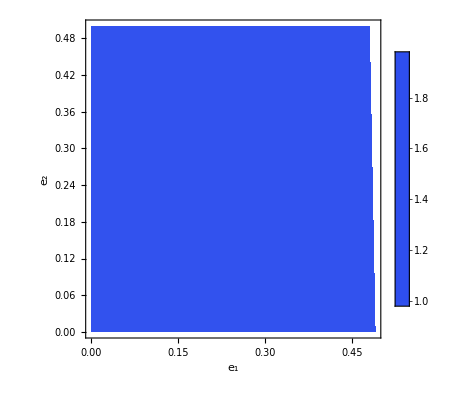

```mathematica
ListDensityPlot[coop,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->24]]
imageSSerrors=Show[SSerrors, ImageSize->Medium];
ListDensityPlot[coop2,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->24]]
imageSSerrors=Show[SSerrors, ImageSize->Medium];
```

```mathematica
Clear["Global`*"]
```

```mathematica
ϵ=(1-e1)*(1-e2)+e1*e2;
{a,b}=Solve[3==(1+Sqrt[(1-ϵ)/(1-e2)] )/(ϵ-e2),e2]
```

{{e2→1/36 (27-6/(1-e1)-(3 √(17-22 e1+9 e1^2))/(√(1-2 e1+e1^2)))},{e2→1/36 (27-6/(1-e1)+(3 √(17-22 e1+9 e1^2))/(√(1-2 e1+e1^2)))}}

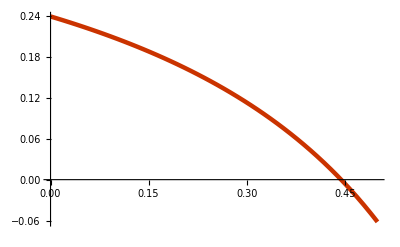

```mathematica
Plot[1/36 (27-6/(1-e1)-(3 √(17-22 e1+9 e1^2))/(√(1-2 e1+e1^2))),{e1,0,0.5}]
```

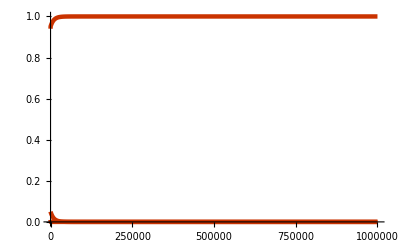

```mathematica
T=1000000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* World 1: B ∅ B *)
w12=(1-g)*ψ*(1-e)*g*(1-ψ); 
w15=g*(1-ψ)*(1-e)*(1-g)*ψ;
w1=Simplify[w15/(w12+w15)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=1;
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w48=g*(1-ψ)*ϵ*g*ψ;
w4=Simplify[w48/(w42+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w65=g*ψ*(1-e)*(1-g)*(1-ψ);
w68=g*ψ*(1-ϵ)*g*ψ;
w6=Simplify[(w65+w68)/(w62+w65+w68)];
(* World 7: G -> B *)
w7=1;
(* World 8: G -> G *)
w8=1;
ψ=0.5;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;
repsys={
gx'[t]==Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t],
gy'[t]==Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t],
gz'[t]==Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t]
};
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
sol=NDSolve[Join[fullsys,{x[0]==0.05,y[0]==0.01,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Plot[{x[t],y[t],1-x[t]-y[t]}/.sol,{t,0,T}]
```

```mathematica
x[T]/.sol
```

{-1.5712×10^-21}

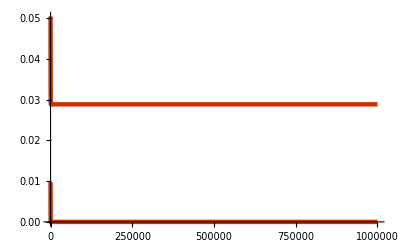

```mathematica
Plot[{x[t],y[t]}/.sol,{t,0,T}]
```

```mathematica
Simple Standing public basin of attraction;
T=100000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* World 1: B ∅ B *)
w12=(1-g)*ψ*(1-e)*g*(1-ψ); 
w15=g*(1-ψ)*(1-e)*(1-g)*ψ;
w1=Simplify[w15/(w12+w15)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=1;
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w48=g*(1-ψ)*ϵ*g*ψ;
w4=Simplify[w48/(w42+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w65=g*ψ*(1-e)*(1-g)*(1-ψ);
w68=g*ψ*(1-ϵ)*g*ψ;
w6=Simplify[(w65+w68)/(w62+w65+w68)];
(* World 7: G -> B *)
w7=1;
(* World 8: G -> G *)
w8=1;
ψ=0.5;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;

pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;

fullsys1={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*(Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*(Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*(Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};

fullsys2={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*((1-g)*(1-e2)+g*ϵ-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*((1-g)*(1-e2)+g*e2-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*((1-g)*(1-e2)+ϵ*g-gz[t])/.{x->x[t],y->y[t]})
};

count=1;
basin=Array[m,{144,3}];
basin1=Array[m,{144,3}];
basin2=Array[m,{144,3}];
Do[
mysum = 0;
mysum1 = 0;
mysum2 = 0;
sys1=fullsys1/.{e1->ii/25,e2->jj/25};
sys2=fullsys2/.{e1->ii/25,e2->jj/25};
Do[
R1=NDSolve[Join[sys1,{x[0]==0.05*i,y[0]==0.05*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",InterpolationOrder->All];
R2=NDSolve[Join[sys2,{x[0]==0.05*i,y[0]==0.05*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",InterpolationOrder->All];
mysum=mysum+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R1[[1]]]-Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R2[[1]]];
mysum1=mysum1+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R1[[1]]];
mysum2=mysum2+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R2[[1]]];
,{i,1,18},{j,1,19-i}];
basin[[count]]={ii/25,jj/25,mysum/171};
basin1[[count]]={ii/25,jj/25,mysum1/171};
basin2[[count]]={ii/25,jj/25,mysum2/171};
count=count+1;
,{ii,1,12},{jj,1,12}];
colfunc=(ColorData["TemperatureMap"][Rescale[#,{0.2,-0.2}]]&);
colfunc2=(ColorData["SunsetColors"][Rescale[#,{0,1}]]&);
imageSimpleStandingBasin=Show[ListDensityPlot[basin,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.2}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
imageSimpleStandingBasin1=Show[ListDensityPlot[basin,InterpolationOrder->0,ColorFunction->colfunc2,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc2,{0,1}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
imageSimpleStandingBasin2=Show[ListDensityPlot[basin,InterpolationOrder->0,ColorFunction->colfunc2,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc2,{0,1}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
Export["public_simple_standing_psi05_basin.pdf",imageSimpleStandingBasin,ImageResolution->400,ImagePadding->0.01];
Export["public_simple_standing_psi05_basin_abductive.pdf",imageSimpleStandingBasin1,ImageResolution->400,ImagePadding->0.01];
Export["public_simple_standing_psi05_basin_nonreasoning.pdf",imageSimpleStandingBasin2,ImageResolution->400,ImagePadding->0.01];
```

```mathematica
imageSimpleStandingBasin1=Show[ListDensityPlot[basin1,InterpolationOrder->0,ColorFunction->colfunc2,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc2,{0,1}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
imageSimpleStandingBasin2=Show[ListDensityPlot[basin2,InterpolationOrder->0,ColorFunction->colfunc2,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc2,{0,1}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
Export["public_simple_standing_psi05_basin.pdf",imageSimpleStandingBasin,ImageResolution->400,ImagePadding->0.01];
Export["public_simple_standing_psi05_basin_abductive.pdf",imageSimpleStandingBasin1,ImageResolution->400,ImagePadding->0.01];
Export["public_simple_standing_psi05_basin_nonreasoning.pdf",imageSimpleStandingBasin2,ImageResolution->400,ImagePadding->0.01];
```

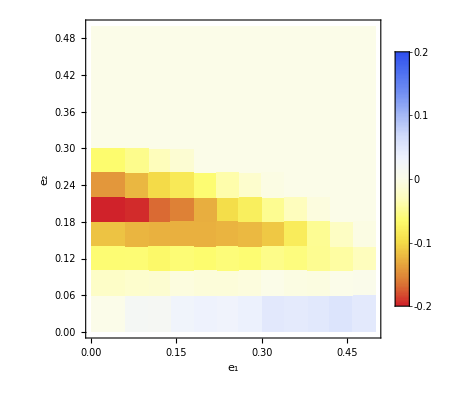

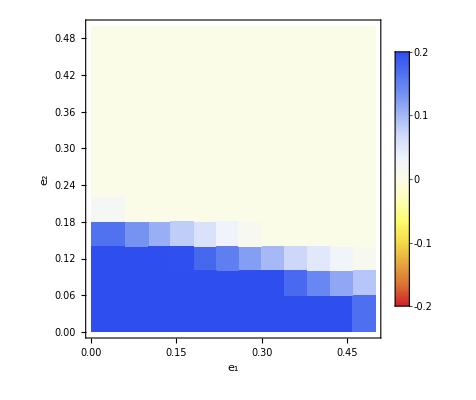

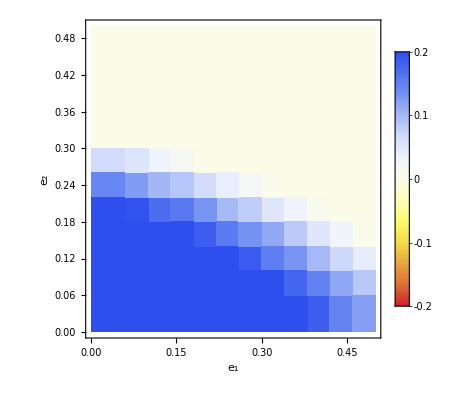

```mathematica
colfunc=(ColorData["TemperatureMap"][Rescale[#,{0.2,-0.2}]]&);
Show[ListDensityPlot[basin,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.2}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}]
Show[ListDensityPlot[basin1,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.2}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}]
Show[ListDensityPlot[basin2,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.2}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}]
```

```mathematica
colfunc=(ColorData["TemperatureMap"][Rescale[#,{0.2,-0.2}]]&);
imageSimpleStandingBasin=Show[ListDensityPlot[basin,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.2}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
Export["public_simple_standing_psi075_basin.pdf",imageSimpleStandingBasin,ImageResolution->400,ImagePadding->0.01];
```

InterpolatingFunction::dmval: Input value {1000.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1000.} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {1000.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1000.} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {1000.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {1000.} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

```mathematica
Simple Standing private basin of attraction;
T=100000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
(* World 1: B ∅ B *)
w12=(1-g)*ψ*(1-e)*g*(1-ψ); 
w15=g*(1-ψ)*(1-e)*(1-g)*ψ;
w1=Simplify[w15/(w12+w15)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=1;
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w48=g*(1-ψ)*ϵ*g*ψ;
w4=Simplify[w48/(w42+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w65=g*ψ*(1-e)*(1-g)*(1-ψ);
w68=g*ψ*(1-ϵ)*g*ψ;
w6=Simplify[(w65+w68)/(w62+w65+w68)];
(* World 7: G -> B *)
w7=1;
(* World 8: G -> G *)
w8=1;
ψ=0.5;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;

pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;

fullsys1={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*((1-gx[t])*(Qbcg*g+Qbcb*(1-g))-gx[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)))/.{x->x[t],y->y[t]}),
gy'[t]==(100000*((1-gy[t])*(Qbdg*g+Qbdb*(1-g))-gy[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)))/.{x->x[t],y->y[t]}),
gz'[t]==(100000*((1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2*g+g2))-gz[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)))/.{x->x[t],y->y[t]}),
gx2'[t]==(100000*((gx[t]-gx2[t])*(Qbcg*g+Qbcb*(1-g))-gx2[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)))/.{x->x[t],y->y[t]}),
gy2'[t]==(100000*((gy[t]-gy2[t])*(Qbdg*g+Qbdb*(1-g))-gy2[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)))/.{x->x[t],y->y[t]}),
gz2'[t]==(100000*((gz[t]-gz2[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb*(1-2*g+g2))-gz2[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)))/.{x->x[t],y->y[t]})
};

fullsys2={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*((1-g)*(1-e2)+g*ϵ-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*((1-g)*(1-e2)+g*e2-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*((1-g)*(1-e2)+g2*ϵ+(g-g2)*e2-gz[t])/.{x->x[t],y->y[t]}),
gx2'[t]==(100000*(gx[t]^2-gx2[t])/.{x->x[t],y->y[t]}),
gy2'[t]==(100000*(gy[t]^2-gy2[t])/.{x->x[t],y->y[t]}),
gz2'[t]==(100000*(gz[t]^2-gz2[t])/.{x->x[t],y->y[t]})
};

count=1;
basin=Array[m,{144,3}];
basin1=Array[m,{144,3}];
basin2=Array[m,{144,3}];
Do[
mysum = 0;
mysum1 = 0;
mysum2 = 0;
sys1=fullsys1/.{e1->ii/25,e2->jj/25};
sys2=fullsys2/.{e1->ii/25,e2->jj/25};
Do[
R1=NDSolve[Join[sys1,{x[0]==0.05*i,y[0]==0.05*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",InterpolationOrder->All];
R2=NDSolve[Join[sys2,{x[0]==0.05*i,y[0]==0.05*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",InterpolationOrder->All];
mysum=mysum+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R1[[1]]]-Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R2[[1]]];
mysum1=mysum1+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R1[[1]]];
mysum2=mysum2+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R2[[1]]];
,{i,1,18},{j,1,19-i}];
basin[[count]]={ii/25,jj/25,(Max[0,mysum1]-Max[0,mysum2])/171};
basin1[[count]]={ii/25,jj/25,Max[0,mysum1]/171};
basin2[[count]]={ii/25,jj/25,Max[0,mysum2]/171};
count=count+1;
,{ii,1,12},{jj,1,12}];
colfunc=(ColorData["TemperatureMap"][Rescale[#,{0.2,-0.2}]]&);
colfunc2=(ColorData["SunsetColors"][Rescale[#,{0,1}]]&);
imageSimpleStandingBasin=Show[ListDensityPlot[basin,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.2}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
Export["private_simple_standing_psi05_basin.pdf",imageSimpleStandingBasin,ImageResolution->400,ImagePadding->0.01];
imageSimpleStandingBasin1=Show[ListDensityPlot[basin1,InterpolationOrder->0,ColorFunction->colfunc2,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc2,{0,1}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
imageSimpleStandingBasin2=Show[ListDensityPlot[basin2,InterpolationOrder->0,ColorFunction->colfunc2,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc2,{0,1}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
Export["private_simple_standing_psi05_basin.pdf",imageSimpleStandingBasin,ImageResolution->400,ImagePadding->0.01];
Export["private_simple_standing_psi05_basin_abductive.pdf",imageSimpleStandingBasin1,ImageResolution->400,ImagePadding->0.01];
Export["private_simple_standing_psi05_basin_nonreasoning.pdf",imageSimpleStandingBasin2,ImageResolution->400,ImagePadding->0.01];
```

```mathematica
colfunc2=(ColorData["SunsetColors"][Rescale[#,{0,0.5}]]&);
imageSimpleStandingBasin=Show[ListDensityPlot[basin,InterpolationOrder->0,PlotRange->{{0,0.5},{0,0.5},{0,0.5}},ColorFunction->colfunc2,PlotLegends->BarLegend[{colfunc2,{0,0.5}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
Export["private_simple_standing_psi05_basin.pdf",imageSimpleStandingBasin,ImageResolution->400,ImagePadding->0.01];
imageSimpleStandingBasin1=Show[ListDensityPlot[basin1,InterpolationOrder->0,PlotRange->{{0,0.5},{0,0.5},{0,0.5}},ColorFunction->colfunc2,PlotLegends->BarLegend[{colfunc2,{0,0.5}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
imageSimpleStandingBasin2=Show[ListDensityPlot[basin2,InterpolationOrder->0,PlotRange->{{0,0.5},{0,0.5},{0,0.5}},ColorFunction->colfunc2,PlotLegends->BarLegend[{colfunc2,{0,0.5}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
Export["private_simple_standing_psi05_basin.pdf",imageSimpleStandingBasin,ImageResolution->400,ImagePadding->0.01];
Export["private_simple_standing_psi05_basin_abductive.pdf",imageSimpleStandingBasin1,ImageResolution->400,ImagePadding->0.01];
Export["private_simple_standing_psi05_basin_nonreasoning.pdf",imageSimpleStandingBasin2,ImageResolution->400,ImagePadding->0.01];
```

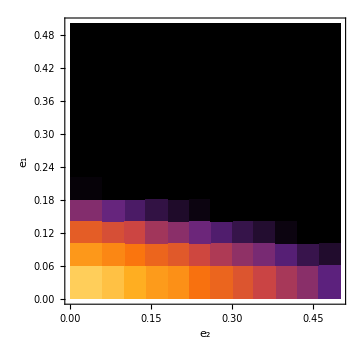
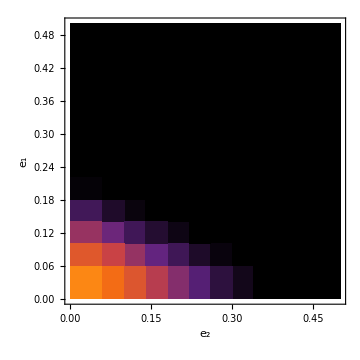
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
colfunc2=(ColorData["SunsetColors"][Rescale[#,{0,0.5}]]&);
imageSimpleStandingBasin=Show[ListDensityPlot[basin,InterpolationOrder->0,PlotRange->{{0,0.5},{0,0.5},{0,0.5}},ColorFunction->colfunc2,PlotLegends->BarLegend[{colfunc2,{0,0.5}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
Export["private_simple_standing_psi05_basin.pdf",imageSimpleStandingBasin,ImageResolution->400,ImagePadding->0.01];
imageSimpleStandingPrivateBasin1=Show[ListDensityPlot[basin1,InterpolationOrder->0,PlotRange->{{0,0.5},{0,0.5},{0,0.5}},ColorFunction->colfunc2,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","Private SS abduction"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSimpleStandingPrivateBasin2=Show[ListDensityPlot[basin2,InterpolationOrder->0,PlotRange->{{0,0.5},{0,0.5},{0,0.5}},ColorFunction->colfunc2,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","Private SS non-reasoning"}},LabelStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSimpleStandingPrivate=Legended[Multicolumn[{imageStayingPublicBasin1,imageStayingPublicBasin2,imageSimpleStandingBasin1,imageSimpleStandingBasin2,imageSimpleStandingBasin1}],Placed[BarLegend[{colfunc2,{0,0.5}},LegendLayout->"Row",LegendMarkerSize->300,LabelStyle->{FontSize->Large},LegendFunction->"Frame",LegendMargins->5],Bottom]]
Export["private_simple_standing_psi05.pdf",imageSimpleStandingPrivate,ImageResolution->400,ImagePadding->0.01];
```

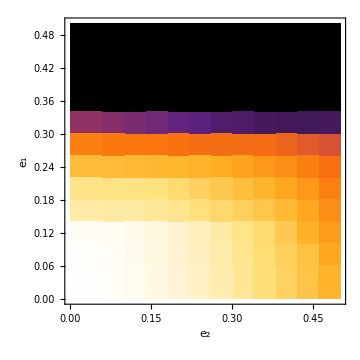
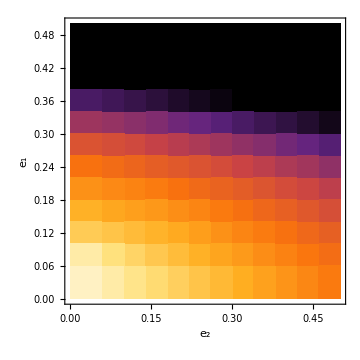
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
imageHeatmaps=Legended[Multicolumn[{imageStayingPublicBasin1,imageStayingPublicBasin2,imageSimpleStandingBasin1,imageSimpleStandingBasin2,imageSimpleStandingBasin1}],Placed[BarLegend[{colfunc2,{0,1}},LegendLayout->"Row",LegendMarkerSize->300,LabelStyle->{FontSize->Large},LegendFunction->"Frame",LegendMargins->5],Bottom]]
Export["heatmaps.pdf",imageHeatmaps,ImageResolution->400,ImagePadding->0.01];
```

```mathematica
Staying public basin of attraction;
T=100000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* World 1: B ∅ B *)
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w48=g*(1-ψ)*ϵ*g*ψ;
w4=FullSimplify[w48/(w42+w48)];
(* World 5: G ∅ B *)
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w68=g*ψ*(1-ϵ)*g*ψ;
w6=FullSimplify[w68/(w62+w68)];
(* World 7: G -> B *)
(* World 8: G -> G *)
w8=1;
ψ=0.5;
Qbdg=(1-e)*w2+e*w4;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdg=(1-e)*w6+e*w8;
Qgcg=ϵ*w8+(1-ϵ)*w6;

pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;

fullsys1={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qgcg*gx[t]+Qbcg*(1-gx[t])-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qgdg*gy[t]+Qbdg*(1-gy[t])-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qgcg*gz[t]+Qbcg*(1-gz[t])-gz[t])/.{x->x[t],y->y[t]})
};

fullsys2={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(g*ϵ-g*gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(g*e2-g*gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(ϵ*g-g*gz[t])/.{x->x[t],y->y[t]})
};

count=1;
basin=Array[m,{144,3}];
basin1=Array[m,{144,3}];
basin2=Array[m,{144,3}];
Do[
mysum = 0;
mysum1 = 0;
mysum2 = 0;
sys1=fullsys1/.{e1->ii/25,e2->jj/25};
sys2=fullsys2/.{e1->ii/25,e2->jj/25};
Do[
R1=NDSolve[Join[sys1,{x[0]==0.05*i,y[0]==0.05*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",InterpolationOrder->All];
R2=NDSolve[Join[sys2,{x[0]==0.05*i,y[0]==0.05*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",InterpolationOrder->All];
mysum=mysum+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R1[[1]]]-Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R2[[1]]];
mysum1=mysum1+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R1[[1]]];
mysum2=mysum2+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R2[[1]]];
,{i,1,18},{j,1,19-i}];
basin[[count]]={ii/25,jj/25,mysum/171};
basin1[[count]]={ii/25,jj/25,Max[0,mysum1]/171};
basin2[[count]]={ii/25,jj/25,Max[0,mysum2]/171};
count=count+1;
,{ii,1,12},{jj,1,12}];
colfunc=(ColorData["TemperatureMap"][Rescale[#,{0.2,-0.2}]]&);
imageStayingPublicBasin1=Show[ListDensityPlot[basin1,InterpolationOrder->0,PlotRange->{{0,0.5},{0,0.5},{0,0.5}},ColorFunction->colfunc2,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","Public St abduction"}},LabelStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageStayingPublicBasin2=Show[ListDensityPlot[basin2,InterpolationOrder->0,PlotRange->{{0,0.5},{0,0.5},{0,0.5}},ColorFunction->colfunc2,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","Public St non-reasoning"}},LabelStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
```

```mathematica
colfunc2=(ColorData["SunsetColors"][Rescale[#,{0,1}]]&);
imageStayingPublicBasin1=Show[ListDensityPlot[basin1,InterpolationOrder->0,PlotRange->{{0,0.5},{0,0.5},{0,1}},ColorFunction->colfunc2,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","Public St abduction"}},LabelStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageStayingPublicBasin2=Show[ListDensityPlot[basin2,InterpolationOrder->0,PlotRange->{{0,0.5},{0,0.5},{0,1}},ColorFunction->colfunc2,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","Public St non-reasoning"}},LabelStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
```

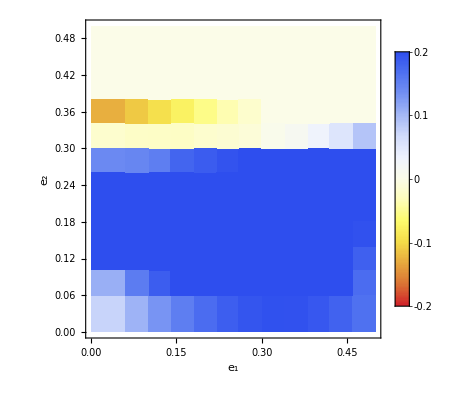

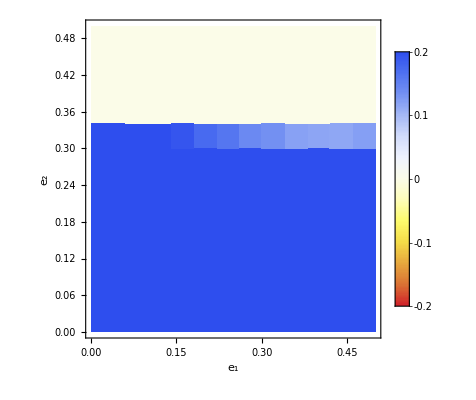

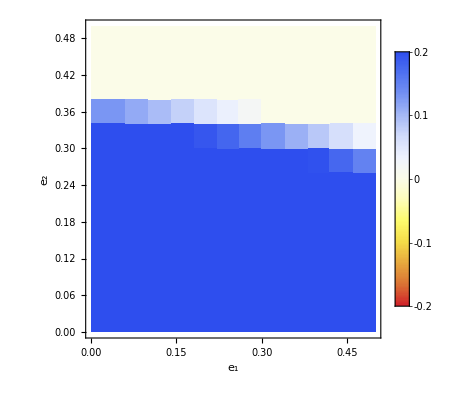

```mathematica
colfunc=(ColorData["TemperatureMap"][Rescale[#,{0.2,-0.2}]]&);
Show[ListDensityPlot[basin,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.2}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}]
Show[ListDensityPlot[basin1,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.2}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}]
Show[ListDensityPlot[basin2,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.2}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}]
```

```mathematica
Staying private basin of attraction;
T=100000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
(* World 1: B ∅ B *)
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w48=g*(1-ψ)*ϵ*g*ψ;
w4=FullSimplify[w48/(w42+w48)];
(* World 5: G ∅ B *)
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w68=g*ψ*(1-ϵ)*g*ψ;
w6=FullSimplify[w68/(w62+w68)];
(* World 7: G -> B *)
(* World 8: G -> G *)
w8=1;
ψ=0.5;
Qbdg=(1-e)*w2+e*w4;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdg=(1-e)*w6+e*w8;
Qgcg=ϵ*w8+(1-ϵ)*w6;

pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;

fullsys1={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*((1-gx[t])*Qbcg-gx[t]*(1-Qgcg))*g/.{x->x[t],y->y[t]}),
gy'[t]==(10000*((1-gy[t])*Qbdg-gy[t]*(1-Qgdg))*g/.{x->x[t],y->y[t]}),
gz'[t]==(10000*((1-gz[t])*(Qbcg*g2+Qbdg*(g-g2))-gz[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2)))/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*((gx[t]-gx2[t])*Qbcg-gx2[t]*(1-Qgcg))*g/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*((gy[t]-gy2[t])*Qbdg-gy2[t]*(1-Qgdg))*g/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*((gz[t]-gz2[t])*(Qbcg*g2+Qbdg*(g-g2))-gz2[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2)))/.{x->x[t],y->y[t]})
};

fullsys2={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(ϵ-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(e2-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(g*e2+g2*(ϵ-e2)-gz[t]*g)/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*(ϵ^2-gx2[t])/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*(e2^2-gy2[t])/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*(gz[t]^2-gz2[t])/.{x->x[t],y->y[t]})
};

count=1;
basin=Array[m,{144,3}];
basin1=Array[m,{144,3}];
basin2=Array[m,{144,3}];
Do[
mysum = 0;
mysum1 = 0;
mysum2 = 0;
sys1=fullsys1/.{e1->ii/25,e2->jj/25};
sys2=fullsys2/.{e1->ii/25,e2->jj/25};
Do[
R1=NDSolve[Join[sys1,{x[0]==0.05*i,y[0]==0.05*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",InterpolationOrder->All];
R2=NDSolve[Join[sys2,{x[0]==0.05*i,y[0]==0.05*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",InterpolationOrder->All];
mysum=mysum+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R1[[1]]]-Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R2[[1]]];
mysum1=mysum1+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R1[[1]]];
mysum2=mysum2+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R2[[1]]];
,{i,1,18},{j,1,19-i}];
basin[[count]]={ii/25,jj/25,mysum/171};
basin1[[count]]={ii/25,jj/25,mysum1/171};
basin2[[count]]={ii/25,jj/25,mysum2/171};
count=count+1;
,{ii,1,12},{jj,1,12}];
colfunc=(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&);
imageStayingBasin=Show[ListDensityPlot[basin,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{0.5,0.5}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
Export["private_staying_psi05_basin.pdf",imageStayingBasin,ImageResolution->400,ImagePadding->0.01];
```

General::munfl: 2.21802×10^-160 2.21802×10^-160 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.59558×10^-159 4.59558×10^-159 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.24683×10^-162 6.24683×10^-162 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

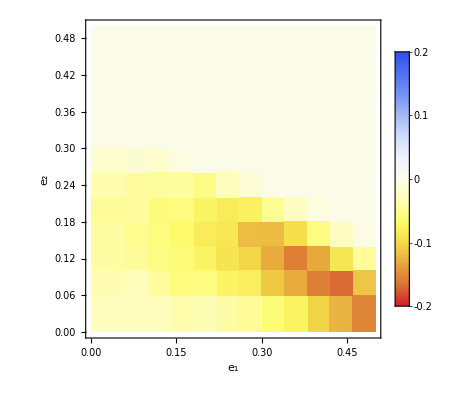

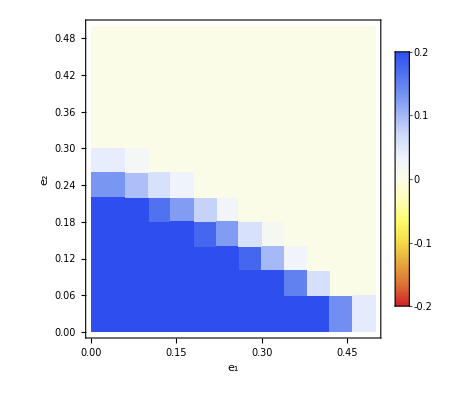

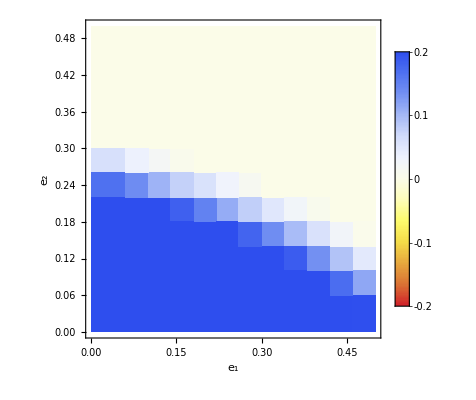

```mathematica
colfunc=(ColorData["TemperatureMap"][Rescale[#,{0.2,-0.2}]]&);
Show[ListDensityPlot[basin,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.2}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}]
Show[ListDensityPlot[basin1,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.2}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}]
Show[ListDensityPlot[basin2,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.2}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}]
```

```mathematica
Stern Judging public basin of attraction;
T=100000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* World 1: B ∅ B *)
w12=(1-g)*ψ*(1-e)*g*(1-ψ); 
w13=(1-g)*ψ*(1-ϵ)*(1-g)*ψ; 
w15=g*(1-ψ)*(1-e)*(1-g)*ψ;
w1=Simplify[w15/(w12+w13+w15)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=0;
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w43=(1-g)*ψ*ϵ*(1-g)*(1-ψ);
w48=g*(1-ψ)*ϵ*g*ψ;
w4=Simplify[w48/(w42+w43+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w65=g*ψ*(1-e)*(1-g)*(1-ψ);
w68=g*ψ*(1-ϵ)*g*ψ;
w6=Simplify[(w65+w68)/(w62+w65+w68)];
(* World 7: G -> B *)
w73=(1-g)*(1-ψ)*ϵ*(1-g)*ψ;
w75=g*ψ*e*(1-g)*ψ;
w78=g*ψ*ϵ*g*(1-ψ);
w7=Simplify[(w75+w78)/(w73+w75+w78)];
(* World 8: G -> G *)
w8=1;
ψ=0.5;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;

pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;

fullsys1={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*(Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*(Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*(Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};

fullsys2={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*(ϵ*g+(1-ϵ)*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*(e2*g+(1-e2)*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*(ϵ*g+(1-e2)*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};

count=1;
basin=Array[m,{144,3}];
basin1=Array[m,{144,3}];
basin2=Array[m,{144,3}];
Do[
mysum = 0;
mysum1 = 0;
mysum2 = 0;
sys1=fullsys1/.{e1->ii/25,e2->jj/25};
sys2=fullsys2/.{e1->ii/25,e2->jj/25};
Do[
R1=NDSolve[Join[sys1,{x[0]==0.05*i,y[0]==0.05*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching",InterpolationOrder->All];
R2=NDSolve[Join[sys2,{x[0]==0.05*i,y[0]==0.05*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching",InterpolationOrder->All];
mysum=mysum+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R1[[1]]]- Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R2[[1]]];
mysum1=mysum1+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R1[[1]]];
mysum2=mysum2+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R2[[1]]];
,{i,1,18},{j,1,19-i}];
basin[[count]]={ii/25,jj/25,(mysum1-mysum2)/171};
basin1[[count]]={ii/25,jj/25,mysum1/171};
basin2[[count]]={ii/25,jj/25,mysum2/171};
count=count+1;
,{ii,1,12},{jj,1,12}];
colfunc=(ColorData["TemperatureMap"][Rescale[#,{0.2,-0.2}]]&);
imageSternJudgingBasin=Show[ListDensityPlot[basin,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.2}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
Export["public_stern_judging_psi05_basin.pdf",imageSternJudgingBasin,ImageResolution->400,ImagePadding->0.01];
```

```mathematica
colfunc=(ColorData["TemperatureMap"][Rescale[#,{0.2,-0.2}]]&);
imageSternJudgingBasin=Show[ListDensityPlot[basin1,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.2}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
Export["public_stern_judging_psi05_basin.pdf",imageSternJudgingBasin,ImageResolution->400,ImagePadding->0.01];
```

ColorData[TemperatureMap][Rescale[#1,{0.4,-0.2}]]&

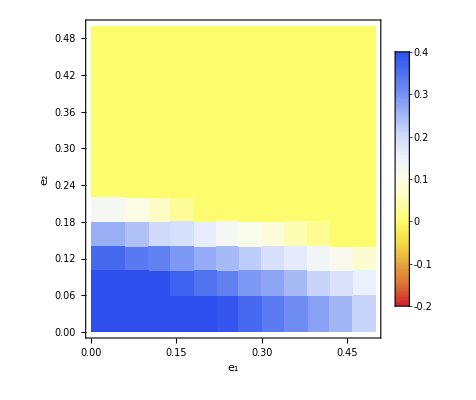

```mathematica
colfunc=(ColorData["TemperatureMap"][Rescale[#,{0.4,-0.2}]]&)
imageSternJudgingBasin=Show[ListDensityPlot[basin1,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.4}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}]
```

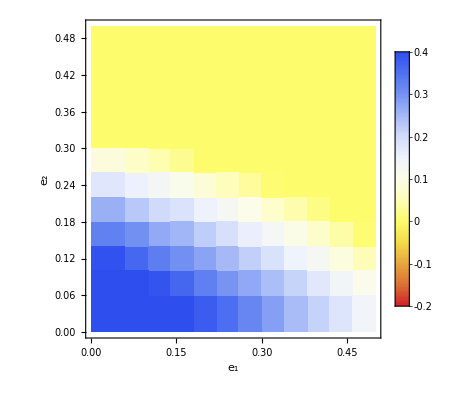

```mathematica
imageSternJudgingBasin=Show[ListDensityPlot[basin2,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.2,0.4}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}]
```

```mathematica
basin
```

```mathematica
colfunc=(ColorData["TemperatureMap"][Rescale[#,{0.5,-0.5}]]&);
imageSternJudgingBasin=Show[ListDensityPlot[basin,InterpolationOrder->0,ColorFunction->colfunc,PlotRange-> {{0,0.5},{0,0.5}},PlotLegends->BarLegend[{colfunc,{-0.5,0.5}}],ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontSize->Large]],Frame->{{True,False},{True,False}}];
Export["public_stern_judging_psi05_basin.pdf",imageSternJudgingBasin,ImageResolution->400,ImagePadding->0.01];
```

```mathematica
Simple Standing private no reasoning
T=1000000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
e1=0.3;
e2=0.02;
repsys={
gx'[t]==(1-g)*(1-e2)+g*ϵ-gx[t],
gy'[t]==(1-g)*(1-e2)+g*e2-gy[t],
gz'[t]==(1-g)*(1-e2)+g2*ϵ+(g-g2)*e2-gz[t],
gx2'[t]==gx[t]^2-gx2[t],
gy2'[t]==gy[t]^2-gy2[t],
gz2'[t]==gz[t]^2-gz2[t]
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->i*0.01,y->j*0.01},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,20},Method->"StiffnessSwitching"];
M[[count]]= {0.01*i,0.01*j,gx[20]/.R[[1]],gy[20]/.R[[1]],gz[20]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*((1-g)*(1-e2)+g*ϵ-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*((1-g)*(1-e2)+g*e2-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*((1-g)*(1-e2)+g2*ϵ+(g-g2)*e2-gz[t])/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*(gx[t]^2-gx2[t])/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*(gy[t]^2-gy2[t])/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*(gz[t]^2-gz2[t])/.{x->x[t],y->y[t]})
};

Eqstable=Array[m,{4851,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.01*i,y[0]==0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",InterpolationOrder->All];
Eqstable[[count]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count=count+1;
,{i,1,98},{j,1,99-i}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
image=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["private_simple_standing_noreasonig_e1_3_e2_02.pdf",image];
```

no private reasoning Simple Standing

```mathematica
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(ϵ-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(e2-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(g*e2+g2*(ϵ-e2)-gz[t]*g)/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*(ϵ^2-gx2[t])/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*(e2^2-gy2[t])/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*(gz[t]^2-gz2[t])/.{x->x[t],y->y[t]})
```

```mathematica
Staying private no reasoning
T=1000000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
e1=0.4;
e2=0.4;
repsys={
gx'[t]==ϵ-gx[t],
gy'[t]==e2-gy[t],
gz'[t]==g*e2+g2*(ϵ-e2)-gz[t]*g,
gx2'[t]==ϵ^2-gx2[t],
gy2'[t]==e2^2-gy2[t],
gz2'[t]==gz[t]^2-gz2[t]
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->i*0.01,y->j*0.01},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,20},Method->"StiffnessSwitching"];
M[[count]]= {0.01*i,0.01*j,gx[20]/.R[[1]],gy[20]/.R[[1]],gz[20]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(ϵ-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(e2-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(g*e2+g2*(ϵ-e2)-gz[t]*g)/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*(ϵ^2-gx2[t])/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*(e2^2-gy2[t])/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*(gz[t]^2-gz2[t])/.{x->x[t],y->y[t]})
};

Eqstable=Array[m,{4851,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.01*i,y[0]==0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",InterpolationOrder->All];
Eqstable[[count]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count=count+1;
,{i,1,98},{j,1,99-i}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
image=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["private_staying_noreasonig_e1_3_e2_02.pdf",image];
```

no private reasoning Staying

```mathematica
Stern judging public nonreasoning
(* ψ=0: w1=1/2, w4, w6=1/2, w7 *)
T=1000000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
repsys={
gx'[t]==ϵ*g+(1-ϵ)*(1-g)-gx[t],
gy'[t]==e*g+(1-e)*(1-g)-gy[t],
gz'[t]==ϵ*g+(1-e)*(1-g)-gz[t]
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,T}];
M[[count]]= {0.01*i,0.01*j,gx[T]/.R[[1]],gy[T]/.R[[1]],gz[T]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(ϵ*g+(1-ϵ)*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(e*g+(1-e)*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(ϵ*g+(1-e)*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{4851,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.01*i,y[0]==0.01*j,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Eqstable[[count]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count=count+1;
,{i,1,98},{j,1,99-i}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
image=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["public_stern_judging_nonreasoning_psi05_e101_e202.pdf",image];
```

judging nonreasoning public Stern

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

General::stop: Further output of NDSolve::ivres will be suppressed during this calculation.

NDSolve::ndcf: Repeated convergence test failure at t == 3.59105; unable to continue.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndcf: Repeated convergence test failure at t == 4.82283; unable to continue.

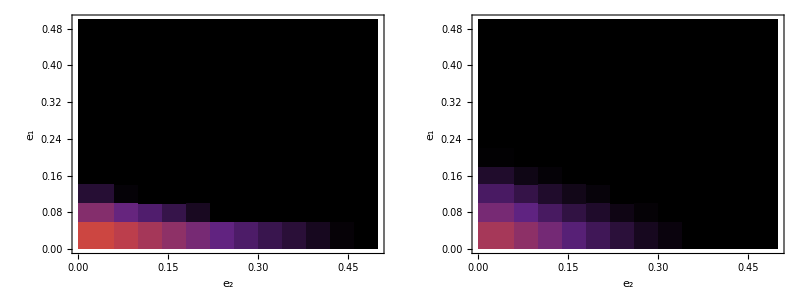

```mathematica
Simple Standing private basin of attraction test;
T=100000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx[t]^2+y*gy[t]^2+(1-x-y)*gz[t]^2;
(* World 1: B ∅ B *)
w12=(1-g)*ψ*(1-e)*g*(1-ψ); 
w15=g*(1-ψ)*(1-e)*(1-g)*ψ;
w1=Simplify[w15/(w12+w15)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=1;
(* World 4: B -> G *)
w42=(1-g)*ψ*e*g*ψ; 
w48=g*(1-ψ)*ϵ*g*ψ;
w4=Simplify[w48/(w42+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=(1-g)*(1-ψ)*(1-e)*g*ψ;
w65=g*ψ*(1-e)*(1-g)*(1-ψ);
w68=g*ψ*(1-ϵ)*g*ψ;
w6=Simplify[(w65+w68)/(w62+w65+w68)];
(* World 7: G -> B *)
w7=1;
(* World 8: G -> G *)
w8=1;
ψ=0.25;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;

pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;

fullsys1={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
0==((1-gx[t])*(Qbcg*g+Qbcb*(1-g))-gx[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)))/.{x->x[t],y->y[t]},
0==((1-gy[t])*(Qbdg*g+Qbdb*(1-g))-gy[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)))/.{x->x[t],y->y[t]},
0==((1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2*g+g2))-gz[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)))/.{x->x[t],y->y[t]}
};

fullsys2={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
0==((1-g)*(1-e2)+g*ϵ-gx[t])/.{x->x[t],y->y[t]},
0==((1-g)*(1-e2)+g*e2-gy[t])/.{x->x[t],y->y[t]},
0==((1-g)*(1-e2)+g2*ϵ+(g-g2)*e2-gz[t])/.{x->x[t],y->y[t]}
};

count=1;
basin=Array[m,{144,3}];
basin1=Array[m,{144,3}];
basin2=Array[m,{144,3}];
Do[
mysum = 0;
mysum1 = 0;
mysum2 = 0;
sys1=fullsys1/.{e1->ii/25,e2->jj/25};
sys2=fullsys2/.{e1->ii/25,e2->jj/25};
Do[
R1=NDSolve[Join[sys1,{x[0]==0.05*i,y[0]==0.05*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"Automatic",InterpolationOrder->All];
R2=NDSolve[Join[sys2,{x[0]==0.05*i,y[0]==0.05*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"Automatic",InterpolationOrder->All];
mysum=mysum+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R1[[1]]]-Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R2[[1]]];
mysum1=mysum1+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R1[[1]]];
mysum2=mysum2+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.R2[[1]]];
,{i,1,18},{j,1,19-i}];
basin[[count]]={ii/25,jj/25,(Max[0,mysum1]-Max[0,mysum2])/171};
basin1[[count]]={ii/25,jj/25,Max[0,mysum1]/171};
basin2[[count]]={ii/25,jj/25,Max[0,mysum2]/171};
count=count+1;
,{ii,1,12},{jj,1,12}];
colfunc2=(ColorData["SunsetColors"][Rescale[#,{0,1}]]&);
imagetest1=Show[ListDensityPlot[basin1,InterpolationOrder->0,PlotRange->{{0,0.5},{0,0.5},{0,1}},ColorFunction->colfunc2,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","Private SS abduction"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imagetest2=Show[ListDensityPlot[basin2,InterpolationOrder->0,PlotRange->{{0,0.5},{0,0.5},{0,1}},ColorFunction->colfunc2,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","Private SS non-reasoning"}},LabelStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imagetest3=Legended[Multicolumn[{imagetest1,imagetest2}],Placed[BarLegend[{colfunc2,{0,1}},LegendLayout->"Row",LegendMarkerSize->300,LabelStyle->{FontSize->Large},LegendFunction->"Frame",LegendMargins->5],Bottom]]
Export["test_psi025.pdf",imagetest,ImageResolution->400,ImagePadding->0.01];
```

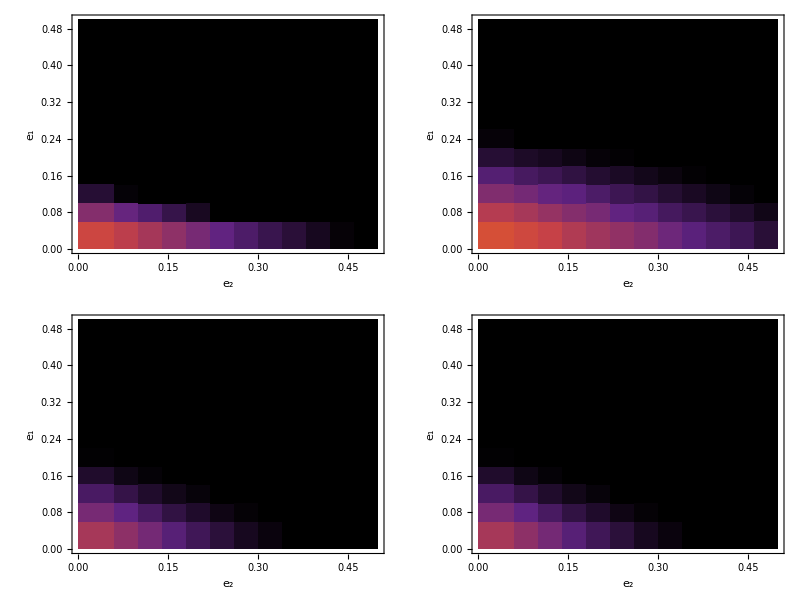

```mathematica
imagetest=Legended[Multicolumn[{imagetest1,imagetest2,imagetest12,imagetest22}],Placed[BarLegend[{colfunc2,{0,1}},LegendLayout->"Row",LegendMarkerSize->300,LabelStyle->{FontSize->Large},LegendFunction->"Frame",LegendMargins->5],Bottom]]
Export["test_psi025.pdf",imagetest,ImageResolution->400,ImagePadding->0.01];
```